# Networks Analysis Brainstorms

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Black,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{ColorData[{"LakeColors","Reverse"}][vertexSyllableList[[i]][[2]]],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.01,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
```

/Users/chipdelmal/Documents/GitHub/MASH-Main/MASH-dev/HectorSanchez/NetworksScripts

RandomPointsPlot

RandomPointsMatrix

## Routine

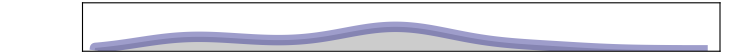
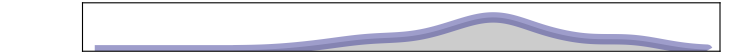
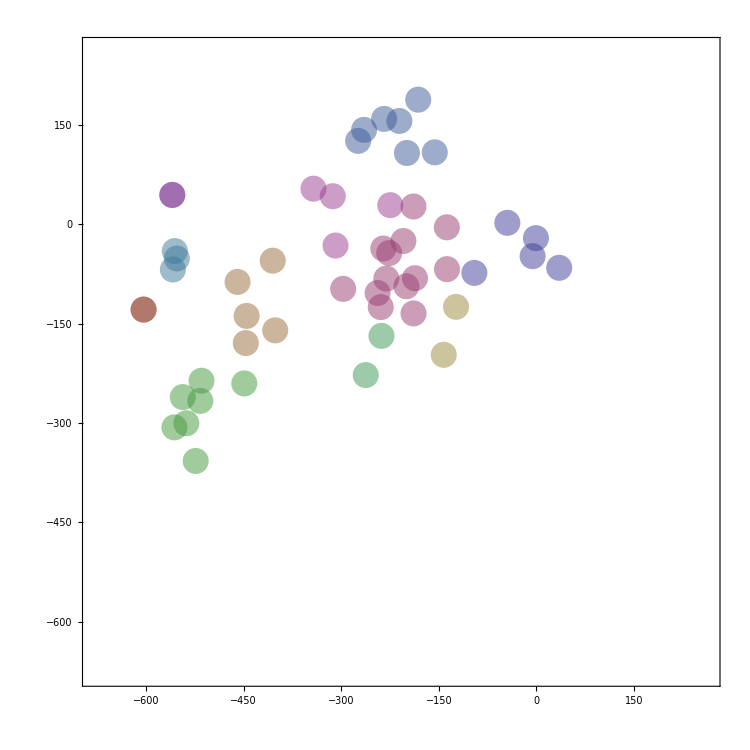
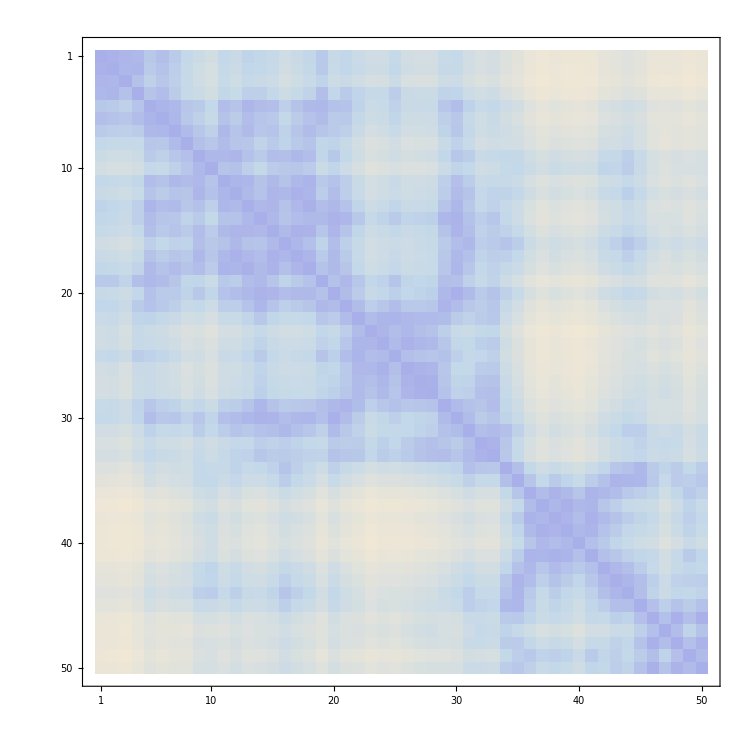
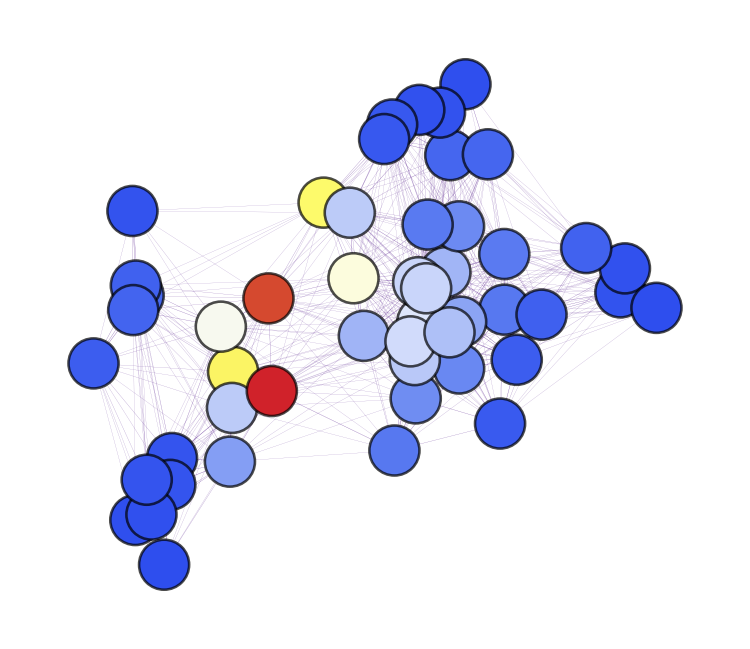
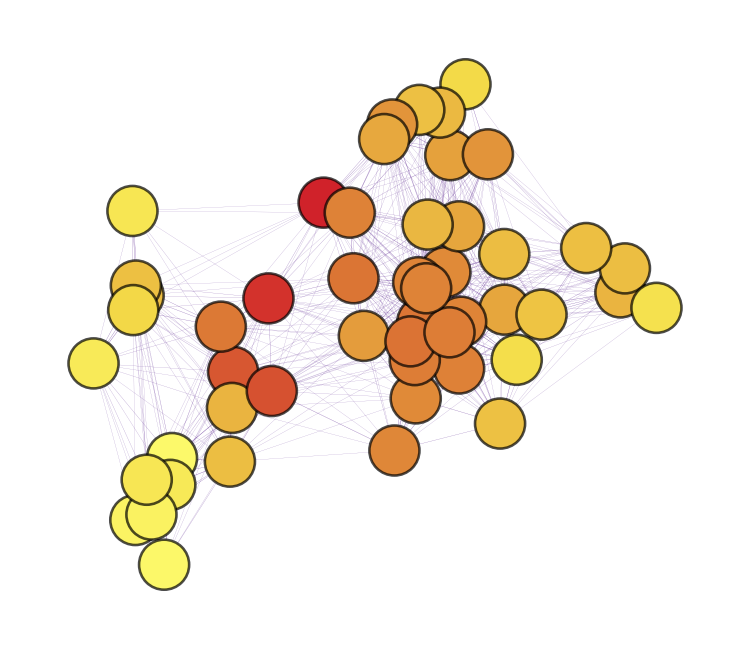
| -Graphics- | 
-Graphics- | -Graphics- |  | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*Generate a random layout*)
citiesDummy = Accumulate[RandomReal[{-100, 100}, {50, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
distances = CalculateEuclideanDistances[citiesDummy];
migration = CalculateMigrationProbabilities[distances, 1000];
{min, max} = {Flatten[citiesDummy] // Min, Flatten[citiesDummy] // Max};
{imageSize, imagePadding, plotRange} = {750, 50, {{min - 75, max + 75}, {0, .005}}};
sampledCoordinates = citiesDummy;
clusteredCoordinates = FindClusters[sampledCoordinates, Method -> "NeighborhoodContraction"];
eucledianDistances = CalculateEuclideanDistances[sampledCoordinates];
(*Calculate distances histograms, matrices and graphs*)
histograms = SmoothHistogramPlot[#, {imageSize, imagePadding}, plotRange] & /@ Transpose[sampledCoordinates];
scatter = ListPlotScatter[clusteredCoordinates, {imageSize, imagePadding}, plotRange];
grid = Grid[{
    {"", Rotate[histograms[[1]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 0 Degree], ""},
    {Rotate[histograms[[2]] // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {0, 0}}] &, 90 Degree], scatter // Show[#, ImagePadding -> {{imagePadding, imagePadding}, {imagePadding, imagePadding}}] &, ""}
    }];
graph = GraphTransitionsFrequenciesWithMax[
   {
    Chop[Quiet[1/eucledianDistances] // ReplacePart[#, {i_, i_} -> 0] &, .004],
    ToString /@ Range[Length[citiesDummy]]
    }, .0001
   ];
graph2 = GraphTransitionsFrequenciesWithMax[
   {
    Chop[Quiet[1/eucledianDistances] // LowerTriangularize // ReplacePart[#, {i_, i_} -> 0] &, .004],
    ToString /@ Range[Length[citiesDummy]]
    }, .0001,
   VertexCoordinates -> ToExpression[citiesDummy],
   LineThickness -> .0000025,
   ImageSize -> 500,
   VertexStyle -> Directive[Lighter[Pink, 0.75], EdgeForm[Directive[Thickness[.0025], Black]]],
   VertexLabelStyle -> Directive[2.5, Opacity[0]],
   VariableStyle -> "Both",
   VertexSize -> 5
   ];
(*Calculate centrality measures and plot*)
cc = BetweennessCentrality[graph];
cc1g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
(*Export["centralityBetweenNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
cc = ClosenessCentrality[graph];
cc2g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
(*Export["centralityClosenessNetwork.png",%,ImageSize->2500,ImageResolution->500];*)
Grid[{{cc1g, cc2g}}];
grid = Grid[{
   {grid, MatrixPlot[eucledianDistances, ColorFunction -> "LakeColors", ImageSize -> imageSize]},
   {cc1g, cc2g}
   }]
(*Export["randomNetworkWithCentrality.png", grid, ImageSize -> 2500, ImageResolution -> 250]*)
```

## Generate Bipartite Network

```mathematica
inMatrix = Chop[Quiet[1/eucledianDistances] // ReplacePart[#, {i_, i_} -> 0] &, .004];
id = RandomChoice[{"A", "B"}, Length[inMatrix]];
mask = Table[
   If[
    id[[i]] == "A",
    ReplaceAll[id, {"A" -> 0, "B" -> 1}],
    ReplaceAll[id, {"A" -> 1, "B" -> 0}]
    ]
   , {i, 1, Length[inMatrix]}];
Prepend[Prepend[mask // Transpose, id] // Transpose, Prepend[id, ""]] // MatrixForm;
style = If[# == "A", Directive[Lighter[Blue, 0.65], EdgeForm[Directive[Thickness[.0025], Black]]], Directive[Lighter[Pink, 0.65], EdgeForm[Directive[Thickness[.0025], Black]]]] & /@ id;
ids = ToString /@ Range[style // Length];
stylesList = (#[[2]] -> #[[1]]) & /@ ({style, ids} // Transpose);

graph = GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask],
   ToString /@ Range[Length[inMatrix]]
   }, .01,
  VertexStyle -> stylesList,
  VertexCoordinates -> sampledCoordinates,
  VertexSize -> 2.5,
  ImageSize -> 750,
  LineThickness -> .0001
  ];
edgeshape2[e_,___]:={Arrowheads[{{.00001,.5}}],Arrow[e]}
graph2= GraphTransitionsFrequenciesWithMax[
  {
   Chop[inMatrix*mask//UpperTriangularize],
   ToString /@ Range[Length[inMatrix]]
   }, .01,
  VertexStyle -> stylesList,
  VertexCoordinates -> sampledCoordinates,
  VertexSize -> 2.5,
  ImageSize -> 750,
  LineThickness -> .001,
EdgeShapeFunction->edgeshape2
  ];
```

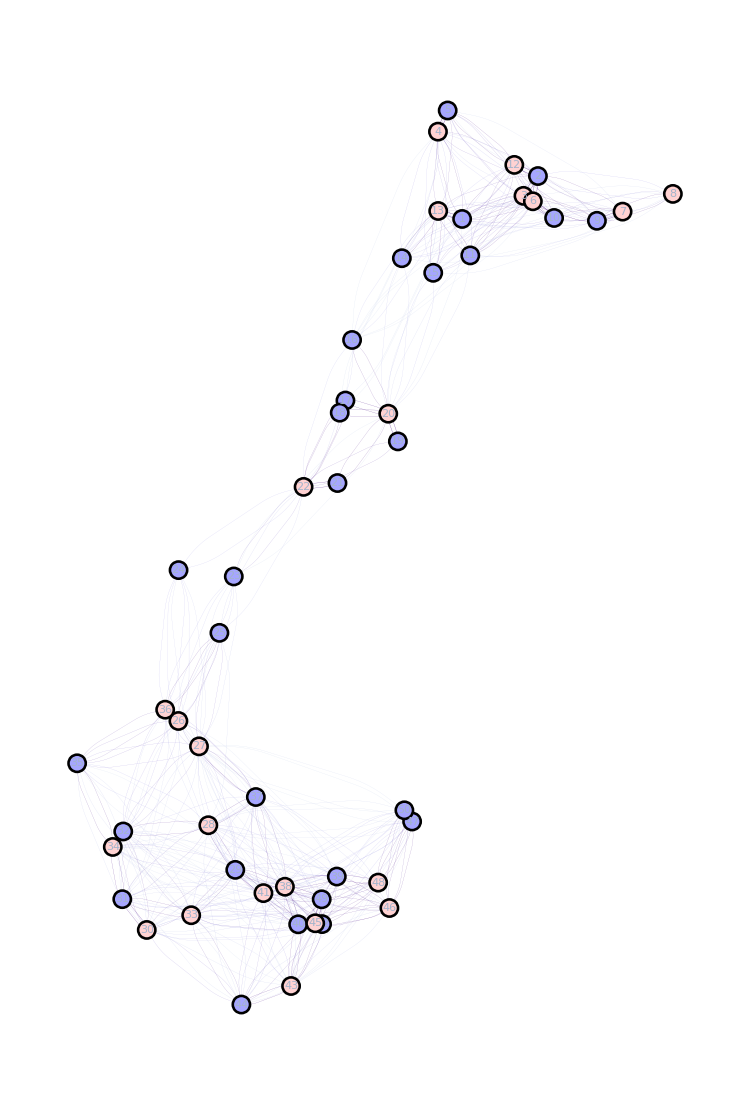
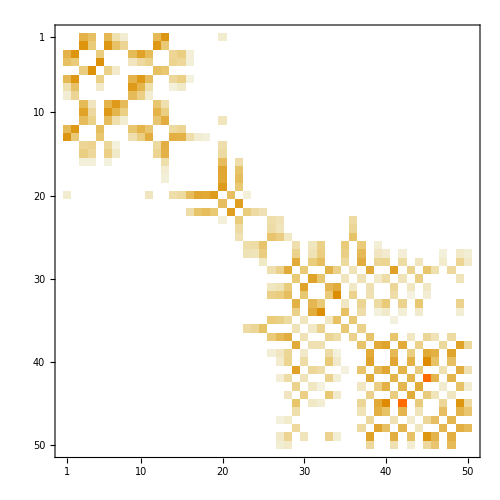
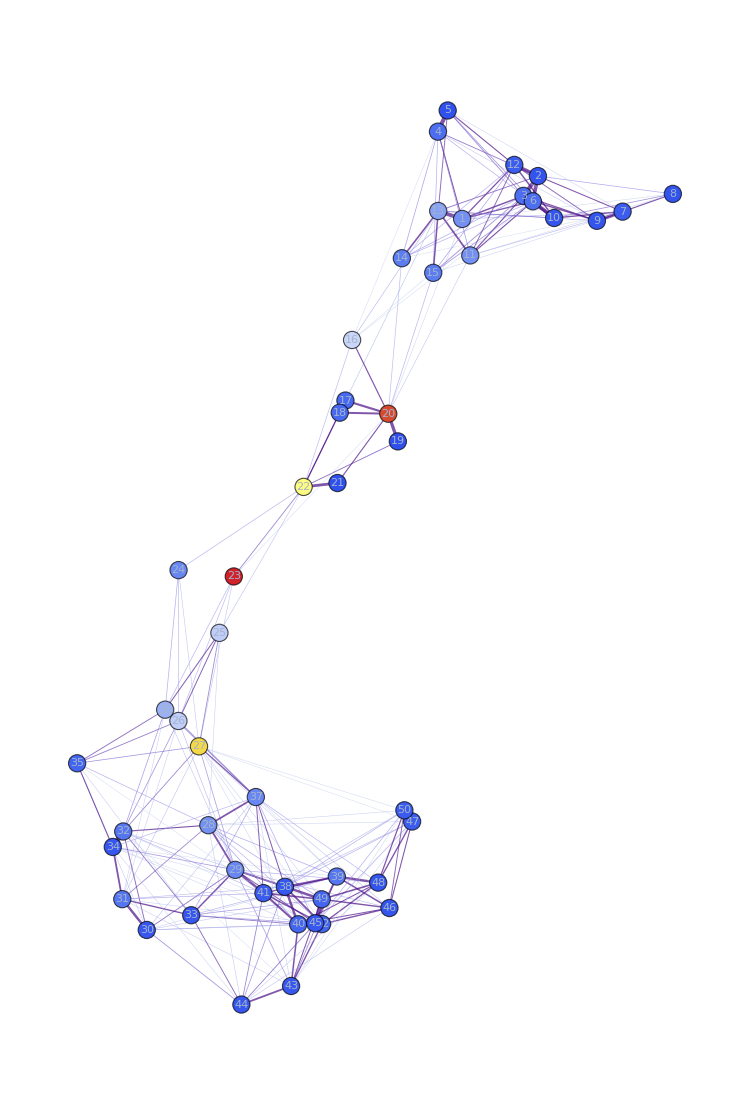
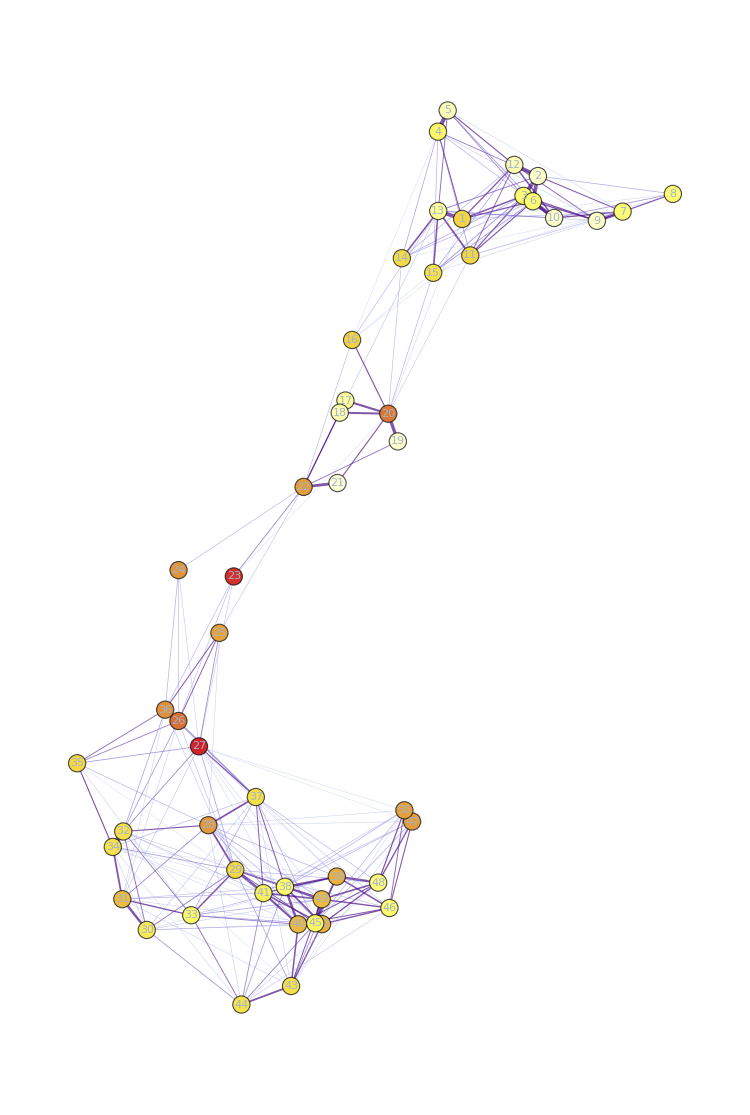
Bipartite Network | Matrix Plot
-Graphics- | -Graphics-
Betwenness | Closeness
-Graphics- | -Graphics-

```mathematica
cc = BetweennessCentrality[graph];
cc1g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
cc = ClosenessCentrality[graph];
cc2g = HighlightGraph[graph2, Table[Style[VertexList[graph][[i]], ColorData["TemperatureMap"][cc[[i]]/Max[cc]]], {i, VertexCount[graph]}], ImageSize -> 750];
Grid[{
Style[#,30]&/@{"Bipartite Network","Matrix Plot"},
{graph,MatrixPlot[inMatrix*mask,ImageSize->500]},
Style[#,30]&/@{"Betwenness","Closeness"},
{cc1g,cc2g}
},Background->{None,{LightBlue,None,LightBlue}},Frame->All]
(*Export["networksGrid.png",%,ImageSize->5000]*)
```

```mathematica
communities=FindGraphCommunities[graph ];
GetCommunitiesInOutTransitionsFrequencies[{inMatrix*mask,ToString/@Range[inMatrix//Length]},communities]
GetCommunitiesInOutTransitionsRatios[{inMatrix*mask,ToString/@Range[inMatrix//Length]},communities]
```

{{1.85533,1.34224,0.475217,0.30842},{0.25489,0.0479833,0.278521,0.0716137}}

{0.879211,0.965485,0.630481,0.81156}